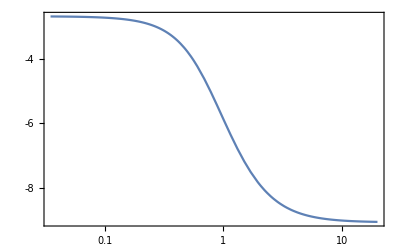

```mathematica
fc=4000;sr=48000;
H=TransferFunctionModel[{{7.1(0.0495053s^2+0.0990107s+0.0495053)/(s^2-1.27951s+0.477529)}},s];
BodePlot[H,PlotLayout->"Magnitude"]
```

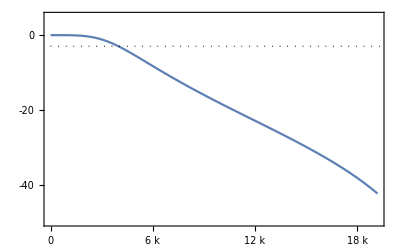

```mathematica
Plot[20Log10@ Abs@(0.0495053(E^{2I (2Pi f)}+2E^{I (2Pi f)}+1)/(E^{2 I (2Pi f)}-1.27951E^{I (2Pi f)}+0.477529)),{f,0,.4}
,PlotRange->{{0,.4},{-50,5}}
,Epilog->{Dotted,Line[{{0,-3},{.5,-3}}]}
,FrameTicks->{{Table[x,{x,-60,0,10}],None},{Table[{x/sr,(x/1000)"k"},{x,0,sr/2,2000}],None}}
,Frame->True]
```